## Steady State Analytical Solutions to Reaction Diffusion Problems

### Notation for partial derivatives in Mathematica:

The following is Mathematica’s way of writing partial derivatives:

c^(0,1)[x,t] 

stands for the first derivative of c with respect to its second argument, i.e. t, thus (∂c)/(∂t), whereas

c^(2,0)[x,t]

stand for the second derivative of c with respect to its first argument, i.e. x, thus (∂^2 c)/(∂x^2).

The easiest way to input these things into Mathematica is either to use the Pallete, or to type in the variable with its arguments, and then apply the differentiation function to it:

```mathematica
D[c[x,t],t]
```

c^(0,1)[x,t]

```mathematica
D[c[x,t], {x,2}]
```

c^(2,0)[x,t]

and so on.

Thus, the following is Mathematica’s way of writing Fick’s second law   (∂c)/(∂t) = D(∂^2 c)/(∂x^2)

c^(0,1)[x,t]==d c^(2,0)[x,t]

It’s best to use lowercase d for the diffusion coefficient because Mathematica uses a capital D to stand for the derivative function and we don’t want to get confused between the two.

Let’s say we want to solve Fick’s law without any other reaction going on.  We need to specify boundary conditions and initial conditions.  

For boundary conditions we can specify the function, the derivative and certain combinations of them.

For example, on the interval 0≤ x ≤ 1, we may take:

c[0,t] = 0, 	c[1,t] =0								(Dirichlet BC)

or

c^(1,0)[0,t] = 0,  c^(1,0)[1,t] = 0			(Flux or Neumann BC)

or

c^(1,0)[0,t] = k(c-cb)					(Robin BC)

c^(1,0)[1,t] = -k(c-cd)

or combinations such as

c^(1,0)[0,t] = 0and c[1,t] ==0

As for initial conditions, we could try c[x,0] = 1.

```mathematica
DSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}, c[x,t], {x, t}]
```

```mathematica
{{c[x,t]->2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0∞}}
```

{{c[x,t]→2 (2 ⅇ^(-1/4 d π^2 t (1+2 K[1])^2) Cos[π K[1]] Cos[1/2 π x (1+2 K[1])])/(π+2 π K[1])K[1]0∞}}

Alas, getting a very helpful solution to such a simple equation is beyond the capabilities of Mathematica.  Let’s try it using NDSolve

```mathematica
Plot3D[Evaluate[c[x,t]/.Flatten[NDSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t], Derivative[1,0][c][0,t]==  0,c[1,t] ==0, c[x,0]== 1}/.d-> 1, c[x,t], {x,0,1}, {t,0,10}]],{t, 0, 10}, {x, 0, 1}, PlotRange-> All,AxesLabel->Automatic ]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

-Graphics3D-

What about the steady state?  In the steady state, the time rate goes to zero and Fick’s law simplifies to

0== c''[x]

To solve we must specify two boundary conditions.  For example we may specify that c[0] = c0 and c[xmax]== 0.

```mathematica
DSolve[{0== c''[x], c[0]==c0, c[xmax]==0}, c[x], x]//FullSimplify
```

{{c[x]→c0-(c0 x)/xmax}}

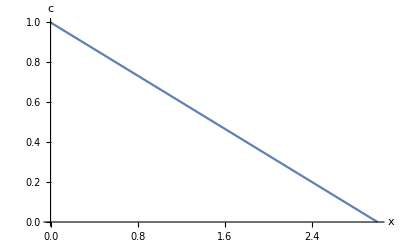

```mathematica
Plot[{Block[{c0=1,xmax=3},c0-c0*x/xmax]},{x,0,3},AxesLabel->{x,c}]
```

We see that we get a line of slope -c0/xmax and y-intercept of c0.  This make sense.  A line is the only function that satisfies 0==c’’[x] for all x.

### Diffusion with uniform decay

c^(0,1)[x,t]==d c^(2,0)[x,t] - k c[x,t]

There is an analytical solution to this, for the right initial and boundary conditions, but Mathematica does not easily find it

```mathematica
DSolve[{Derivative[0,1][c][x,t]==d Derivative[2,0][c][x,t]-k c[x,t],Derivative[1,0][c][0,t]==  1,c[1,t] ==0, c[x,0]== 0}, c[x,t], {x, t}]
```

DSolve[{c^(0,1)[x,t]==-k c[x,t]+d c^(2,0)[x,t],c^(1,0)[0,t]==1,c[1,t]==0,c[x,0]==0},c[x,t],{x,t}]

In the steady state, however, the time rate goes to zero and this simplifies greatly:

0==d c''[x]- k c[x]

If we divide by k, we can see that the result, whatever it is, can only depend upon the ratio d/k, and not d or k separately.  We will define a new “lumped” parameter λ = √(d/k); in this case the above equation can be re-written as

0==λ^2 c''[x]-  c[x]

This can only be solved by specifying two boundary conditions.  For example, we may specify that c[0] = c0 and c[xmax]== 0

```mathematica
DSolve[{0==λ^2 C''[x]-  C[x], C[0]==C0, C[xmax]==0}, C[x], x]//Simplify
```

{{C[x]→(C0 ⅇ^(-x/λ) (-ⅇ^((2 x)/λ)+ⅇ^((2 xmax)/λ)))/(-1+ⅇ^((2 xmax)/λ))}}

This equation is fairly compact, but we can make it simpler.  Notice that x and xmax only ever appear as a ratio with λ.  We may define X = x/λ and Xmax as xmax/λ; 

At the same time, we can define C[x] as c[x]/c0.  Then the above equation can be written as

```mathematica
C[X]->(ⅇ^-X (-ⅇ^(2 X)+ⅇ^(2 Xmax)))/(-1+ⅇ^(2 Xmax))
```

C[X]→(ⅇ^-X (-ⅇ^(2 X)+ⅇ^(2 Xmax)))/(-1+ⅇ^(2 Xmax))

There are also functions called Hyperbolic Trigonometric Functions that represent combinations of exponentials; sometimes these equations can be made even simpler looking by writing them in terms of such functions.  When you call “FullSimplify”, Mathematica searches for such simplifications.

```mathematica
FullSimplify[C[X]->(ⅇ^-X (-ⅇ^(2 X)+ⅇ^(2 Xmax)))/(-1+ⅇ^(2 Xmax))]
```

C[X]→Cosh[X]-Coth[Xmax] Sinh[X]

Note that there the only dependence upon Xmax is through Coth. Recall the definitions of the hyperbolic functions.

```mathematica
TrigToExp[Cosh[x]]
```

ⅇ^-x/2+ⅇ^x/2

```mathematica
TrigToExp[Coth[x]]
```

(ⅇ^-x+ⅇ^x)/(-ⅇ^-x+ⅇ^x)

```mathematica
TrigToExp[Sinh[x]]
```

-ⅇ^-x/2+ⅇ^x/2

### Visualizing the result.

Let’s visualize the result using Manipulate.

```mathematica
Manipulate[Plot[Cosh[X]-Coth[Xmax] Sinh[X], {X, 0, Xmax}, PlotRange-> {{0, 10},All}], {{Xmax, 0.1}, 10^-6, 10}]
```

We see that when Xmax is small, the result is much like the case when there is just diffusion and no reaction.  As Xmax grows, the result approaches a limiting shape that stops depending upon Xmax, except at the very edge of the shape.  This is because:

```mathematica
Limit[Coth[Xmax],Xmax->Infinity]
```

1

### Diffusion with uniform decay and an infinitely far boundary

A useful case to examine is when Xmax is so far away it is effectively at infinity.  You cannot put infinity in as a boundary position, but you can  take the limit as you let Xmax go to infinity.

```mathematica
C[X]->Limit[(ⅇ^-X (-ⅇ^(2 X)+ⅇ^(2 Xmax)))/(-1+ⅇ^(2 Xmax)), Xmax-> ∞]
```

C[X]→ⅇ^-X

replacing X with its definition of x/λ , and C[X] with its definition, c[x]/c0, we get:

```mathematica
C[x]== C0 ⅇ^(-x/λ)
```

C[x]==C0 ⅇ^(-x/λ)

which is the steady state solution for diffusion with uniform decay from a fixed boundary on an infinite domain.

```mathematica
Cosh[x]-Sinh[x]//FullSimplify
```

ⅇ^-x